# Übungsblatt 5

```mathematica
ClearAll[Γ,h,β,M]
```

## Aufgabe 1

(b)

```mathematica
Γ=2.5(*GeV*);
h[e_,M_]:=1/((e^2-M^2)^2+M^2*Γ^2);
```

```mathematica
β=1/Integrate[h[e,91.2],{e,1,150}]
```

13273.9

(h)

```mathematica
daten=Import["C:/Users/olive/bwSyncShare/Documents/Dokumente/Physik/5. Semester/Programmieren und Rechnernutzung/Bayes-Statistik/spectrum.txt","Table"];
```

```mathematica
daten[[1]]
```

{61.8559165976057912}

```mathematica
logLBbest=−3730.35;
logLCbest=-3730.26;
fB[dat_,b_,M_]:=b*0.27097138638119556*dat^-1.1+(1-b)*β/((dat^2-M^2)^2+2.5^2*M^2);
logL[b_]:=Total[Log[fB[daten,b,91]]];
```

```mathematica
logZB=logLBbest+Log[Integrate[Exp[logL[b]-logLBbest],{b,0,1}]]
```

{-3607.08+3.14159 ⅈ}

```mathematica
Integrate[Exp[logL[b]-logLBbest],{b,0.9,1}]
```

{-3.41448×10^53}

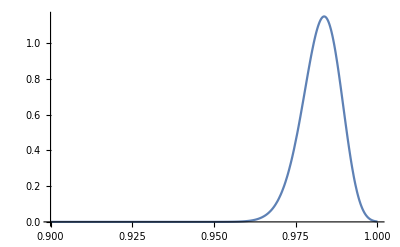

```mathematica
Plot[Exp[logL[b]-logLBbest],{b,0.9,1},PlotRange->All]
```